```mathematica
3!
```

6

```mathematica
f[n_,m_]:=(n!)/((n-m)!n^m)
```

```mathematica
f[3,2]
```

2/3

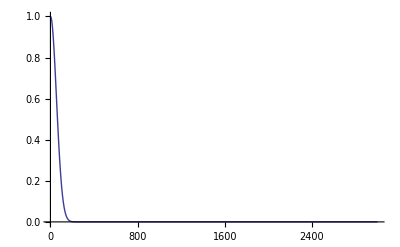

```mathematica
Plot[f[3000,x],{x,1,3000},PlotRange->Full]
```

```mathematica
f[n,m]/f[n,m-1]
```

((1-m+n)!)/(n (-m+n)!)

```mathematica
f[n,n]
```

n^-n n!

```mathematica
f[n,n-1]
```

n^(1-n) n!

```mathematica
f[n,n-m]
```

(n^(m-n) n!)/(m!)

```mathematica
(1+x)^n
```

(1+x)^n

```mathematica
Expand[%]
```

(1+x)^n

```mathematica
Sum[1/n^2,{n,0,s]]
```

```mathematica
Simplify[Sum[Binomial[n,i],{i,0,p}],p
```

2^n-Binomial[n,1+p] Hypergeometric2F1[1,1-n+p,2+p,-1]

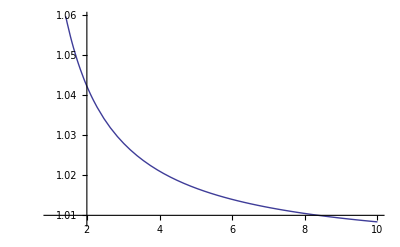

```mathematica
Plot[n!/(n^n Exp[-n](2Pi n)^(1/2)),{n,1,10}]
```

```mathematica
al1=n*m/(n-m+1)
```

(m n)/(1-m+n)

```mathematica
pn=1/(al1^2m!(n-m)n^m)
```

```mathematica
p[m_,j_]:=Product[i/m,{i,j,2m}]
```

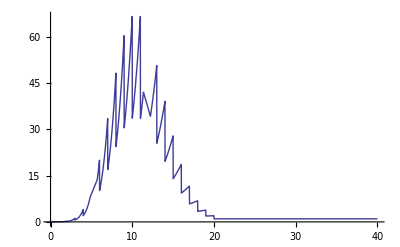

```mathematica
Plot[p[10,x],{x,0,40}]
```

```mathematica
Sum[a^l(1-a)^(n-l),{l,0,n}]
```

(-(1-a)^n+(1-a)^n a+a^(1+n))/(-1+2 a)

```mathematica
Simplify[%]
```

(-(1-a)^n+(1-a)^n a+a^(1+n))/(-1+2 a)

```mathematica
Factor[%]
```

(-(1-a)^n+(1-a)^n a+a^(1+n))/(-1+2 a)

```mathematica
Sum[a^l,{l,0,n}]
```

(-1+a^(1+n))/(-1+a)

```mathematica
Sum[a^(l+p)s^(n-l),{l,0,n-p}]
```

(-a^p s^(1+n)+a^(1+n) s^p)/(a-s)

```mathematica
Sum[a^(l+1)s^(n-1),{l,0,n-1}]
```

(a (-1+a^n) s^(-1+n))/(-1+a)

```mathematica
Sum[a^(l+0)(1-a)^(n-0),{l,0,n-0}]
```

((1-a)^n (-1+a^(1+n)))/(-1+a)

```mathematica
%/.s->1-a
```

((1-a)^n (-1+a^(1+n)))/(-1+a)

```mathematica
D[%,a,s]
```

(a^n n)/(a-s)+(a^n n s)/(a-s)^2+(a n s^n)/(a-s)^2-(n s^n)/(a-s)-(a (a^n-s^n))/(a-s)^2+(a^n-s^n)/(a-s)-(2 a s (a^n-s^n))/(a-s)^3+(s (a^n-s^n))/(a-s)^2

```mathematica
Simplify[%]
```

(a^(2+n) n-a^(1+n) (2+n) s+a (2+n) s^(1+n)-n s^(2+n))/(a-s)^3

```mathematica
FullSimplify[%/.(s->1-a)]
```

(a^(1+n) (-2-n+2 a (1+n))+(1-a)^(1+n) (-n+2 a (1+n)))/(-1+2 a)^3

```mathematica
%/.{a->1}
```

-2-n+2 (1+n)+0^(1+n) (-n+2 (1+n))

```mathematica
Simplify[%]
```

2 0^(1+n)+n+0^(1+n) n

```mathematica
(a^(1+n) (-2-n+2 a (1+n))+(1-a)^(1+n) (-n+2 a (1+n)))/(-1+2 a)^3/.a->0
```

-0^(1+n) (-2-n)+n

```mathematica
Product[(1+i/n),{i,0,n/2}]
```

(1/n)^(n/2) Pochhammer[1+n,n/2]

```mathematica
Limit[Log[%],n->Infinity]
```

∞

```mathematica
ff=al2(1-gm)/N2(m+1-N1)(N2-m+N1)/(m+1)^2
```

(al2 (1-gm) (1+m-N1) (-m+N1+N2))/((1+m)^2 N2)

```mathematica
cond={gm->0.01,N2->10000,N1->1000000}
```

{gm→0.01,N2→10000,N1→1000000}

```mathematica
ff/.cond
```

(0.00099 al2 (101000-m) (-99999+m))/(1+m)^2

```mathematica
Solve[((ff/.{m->N1+N2*0.1}/.cond))==1,al2]
```

{{al2→1.12346×10^9}}

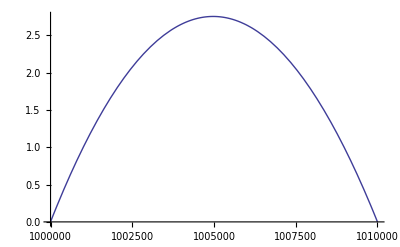

```mathematica
Plot[(ff/.cond)/.al2->1.1234590347934895*^9,{m,N1/.cond,(N1+N2)/.cond}]
```

```mathematica
Solve[4.791661259204518*^-9 al2==1,
```

```mathematica
Integrate[t^2/((t t-a)^2+b^2),{t,0,1}]
```

If[(√(a-ⅈ b) Im[√(a-ⅈ b)]≠0||Im[a]^2+4 Im[b]+4 Re[a]+Re[b]^2≥4+2 Im[a] Re[b]||(Im[b]+Re[a]<0&&Im[a]==Re[b]))&&(((Re[√(a+ⅈ b)]≥1||(Re[√(a+ⅈ b)]≤0&&(Im[b]≥Re[a]||Im[a]+Re[b]≠0)))&&√(a+ⅈ b)≠0)||√(a+ⅈ b)∉Reals),(ⅈ (√(-a-ⅈ b) ArcTan[1/(√(-a-ⅈ b))]-√(-a+ⅈ b) ArcTan[1/(√(-a+ⅈ b))]))/(2 b),Integrate[t^2/(b^2+(a-t^2)^2),{t,0,1},Assumptions→!((√(a-ⅈ b) Im[√(a-ⅈ b)]≠0||Im[a]^2+4 Im[b]+4 Re[a]+Re[b]^2≥4+2 Im[a] Re[b]||(Im[b]+Re[a]<0&&Im[a]==Re[b]))&&(((Re[√(a+ⅈ b)]≥1||(Re[√(a+ⅈ b)]≤0&&(Im[b]≥Re[a]||Im[a]+Re[b]≠0)))&&√(a+ⅈ b)≠0)||√(a+ⅈ b)∉Reals))]]

```mathematica
Integrate[(t/((t-a)^2+b^2))^(1/2),{t,0,1}]
```

$Aborted

```mathematica
(t/((t-a)^2+b^2))^(1/2)
```

√(t/(b^2+(-a+t)^2))

```mathematica
Plot[
```